# Solutions to Selected Problems

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

## Quantum Computation: Overview

This constructs the desired quantum circuit model.

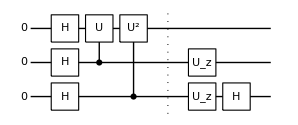

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2,3}],S[{1,2,3},6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"],ControlledU[S[3],Rotation[2ϕ,S[1,1]],"Label"->"U^2"],"Separator",{Rotation[0,S[2,3]],Rotation[Pi/2,S[3,3]]},S[3,6]]
```

```mathematica
out=ExpressionFor[qc]//TrigToExp//Simplify;
LogicalForm[QuissoFactor@out/.ϕ->Pi/2,S@{1,2}]
```

((1/4+ⅈ/4) ⅇ^(-(3 ⅈ π)/4) (0_S_1+1_S_1)⊗(ⅇ^((ⅈ π)/4) 0_S_2+1_S_2)⊗(2 0_S_3))/(√2)

## Quantum Algorithms: Introduction

Here is a particular classical oracle.

```mathematica
f[0,0]=0
f[0,1]=0
f[1,0]=1
f[1,1]=0
```

0

0

1

0

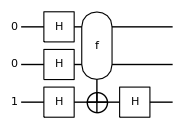

1_S_3⊗(1/2 0_S_10_S_2+1/2 0_S_11_S_2-1/2 1_S_10_S_2+1/2 1_S_11_S_2)

```mathematica
cc={1,2};
tt={3};
ct=Join[cc,tt];
qc=QuantumCircuit[
LogicalForm[Ket[S[tt]->1],S[ct]],
S[ct,6],
Oracle[f,S@cc,S@tt],
S[tt,6]
]
out=ExpressionFor[qc];
QuissoFactor[out,S[tt]]//LogicalForm
```

```mathematica
bb=f@@@IntegerDigits[Range[0,2^2],2,2]
```

{0,0,1,0,0}

Here is a particular classical oracle.

```mathematica
f[0,0]={0,1}
f[0,1]={1,0}
f[1,0]={0,1}
f[1,1]={1,1}
```

{0,1}

{1,0}

{0,1}

{1,1}

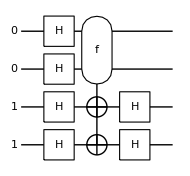

1_S_31_S_4⊗(-1/2 0_S_10_S_2-1/2 0_S_11_S_2-1/2 1_S_10_S_2+1/2 1_S_11_S_2)

```mathematica
cc={1,2};
tt={3,4};
ct=Join[cc,tt];
qc=QuantumCircuit[
LogicalForm[Ket[S[tt]->1],S[ct]],
S[ct,6],
Oracle[f,S@cc,S@tt],
S[tt,6]
]
out=ExpressionFor[qc];
QuissoFactor[out,S[tt]]//LogicalForm
```

```mathematica
bb=f@@@IntegerDigits[Range[0,2^2],2,2]
```

{{0,1},{1,0},{0,1},{1,1},{0,1}}